```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
<<"qtools.wl"
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 8050, lb->0.5, la->1.5};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;
```

```mathematica
(*For the purpose of computation of inertia of the top plate assume that the top plate is regular. We know the Iz from https://en.wikipedia.org/wiki/List_of_moments_of_inertia and from perpendicular axis theorem we get itpx and itpy and assumed to be completely planar*)
```

```mathematica
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->8050, t->0.01}/.datap;
tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;
itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;
```

```mathematica
(*tpdat = {c1->0.1, c2->0.1, c3->0, x->0, y->0, z->1.1};*)
```

```mathematica
(*Assuming manipulator is symmetric in construction*)
```

```mathematica
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
```

```mathematica
(*Locations of all the known ground joints*)
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];
```

```mathematica
al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
```

```mathematica
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
```

```mathematica
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
```

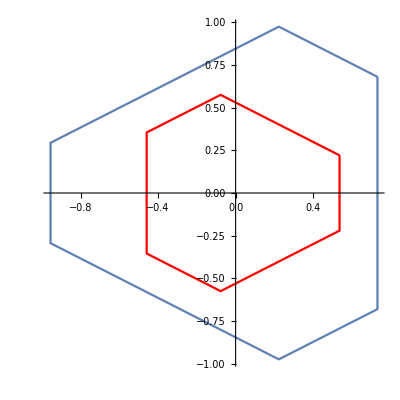

```mathematica
Show[ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]]],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Red], AspectRatio->1]
```

```mathematica
(*Variables*)
```

```mathematica
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
l = Table[Symbol["l"<>ToString[i]],{i,6}];
```

```mathematica
(*Assume the center of the top plate and the orientation as p and R*)
```

```mathematica
pc = {x, y, z};
qq = Join[ϕ, ψ, l];
qx = Join[pc, {c1, c2, c3}];
q = Join[qx, qq];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
```

```mathematica
(*Checking the orthogonolity of the rotation matrix*)
```

```mathematica
Simplify[Rtp.T[Rtp]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Jvtp = D[pc, {q}];
Jωtp = SkewMat2vec[Simplify[T[Rtp].D[Rtp,{q}]]];
```

```mathematica
(*Formulating the dynamics equations of the manipulator*)
```

```mathematica
(*Finding the Jvp for the ai parts of the links*)
```

```mathematica
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
```

```mathematica
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
```

```mathematica
Jpai = D[pa, {q}];
Jpbi = D[pb, {q}];
```

```mathematica
(*To generate the test data for this system*)
```

```mathematica
qqrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
qxrule = {x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]};
qrule = Join[qxrule,qqrule];
```

```mathematica
(*Angular velocity of any leg li*)
```

```mathematica
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
Jωl = Table[SkewMat2vec[T[Rl[[i]]].D[Rl[[i]],{q}]],{i, 6}];
```

```mathematica
(*Mass Matrix*)
```

```mathematica
tempM = Append[(Table[T[Jpai[[i]]].Jpai[[i]]*ma+T[Jpbi[[i]]].Jpbi[[i]]*mb+T[Jωl[[i]]].Ibi.Jωl[[i]]+T[Jωl[[i]]].Iai.Jωl[[i]],{i, 6}]), T[Jvtp].Jvtp*mtp+T[Jωtp].Itp.Jωtp];
tempM//dim
```

{7,24,24}

```mathematica
tempM2 = Total[tempM, {1}];
tempM2//dim
```

{24,24}

```mathematica
tempM2 - T[tempM2]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
tempM2//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,la,lb,ma,mb,mtp,ri,ro,rt,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
Mmat = Simplify[tempM2/.qrule/.datap/.leglparam/.legmparam/.tpmparam];
```

```mathematica
Mmat//Variables
```

{c1[t],c2[t],c3[t],Cos[2 ψ1[t]],Cos[2 ψ2[t]],Cos[2 ψ3[t]],Cos[2 ψ4[t]],Cos[2 ψ5[t]],Cos[2 ψ6[t]],l1[t],l2[t],l3[t],l4[t],l5[t],l6[t]}

```mathematica
size[Mmat]
```

Size of the expression is:32.0938 KB.

```mathematica
qt = q/.qrule;
```

```mathematica
tic[]
n = Length[qt];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii= 1, ii≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], qt[[kk]]] + D[Mmat[[ii,kk]], qt[[jj]]] - D[Mmat[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 0.240337 seconds.

CPU time consumed: 0.234 seconds.

```mathematica
sampledat = {ϕ1[t]->-0.4120776809584599,ϕ2[t]->-0.5171397464399574,ϕ3[t]->0.17764187369764603,ϕ4[t]->0.28736859806179627,ϕ5[t]->0.19195198975076458,ϕ6[t]->0.3314663928113124,ψ1[t]->-0.010571279864228872,ψ2[t]->0.00656986783518712,ψ3[t]->0.2888385292898862,ψ4[t]->0.45146664507018724,ψ5[t]->-0.32862234369207344,ψ6[t]->-0.5474095601531795,l1[t]->1.0763732914509816,l2[t]->1.3589653226424672,l3[t]->1.3306253991320864,l4[t]->1.3670902994040683,l5[t]->1.1391099344974789,l6[t]->1.163106217592093};
```

```mathematica
initvel = {ϕ1'[t]->0.04819125830959889,ϕ2'[t]->0.03427428403166,ϕ3'[t]->0.022537110420045366,ϕ4'[t]->-0.02504333390626954,ϕ5'[t]->-0.06015570745871055,ϕ6'[t]->-0.06962346394226754,ψ1'[t]->0.17522543152669445,ψ2'[t]->0.09442759444255354,ψ3'[t]->0.05971195202706652,ψ4'[t]->0.04189876317323693,ψ5'[t]->0.08197436457283205,ψ6'[t]->0.1734108446847269,l1'[t]->0.1,l2'[t]->0,l3'[t]->0,l4'[t]->0,l5'[t]->0,l6'[t]->0};
```

```mathematica
Mmatdat = D[Mmat, t];
tempA = Mmatdat-2*tempC;
temppA = tempA+T[tempA];
temppA//dim
Chop[Simplify[temppA]]
```

{24,24}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*Formulating the potential term*)
```

```mathematica
tempV = Table[{ma*g*pa[[i]][[3]], mb*g*pb[[i]][[3]]},{i, 6}];
```

```mathematica
V = Total[Append[Flatten[tempV], mtp*g*pc[[3]]]]/.datap/.leglparam/.legmparam/.tpmparam;
G = D[V, {q}];
```

```mathematica
Variables[G]
```

{l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
(*Now we have dynamics in the extended configuration space. We need to map it back to the task space of the manipulator*)
```

```mathematica
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating the simple constraint equations (not the rigidity of the top platform constraint)*)
```

```mathematica
η = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
(*ηleg = Table[Together[((atps-b)[[i]]).((atp-b)[[i]])-l[[i]]^2],{i, 6}];*)
```

```mathematica
(*ηtask = Join[η, ηleg]/.alsrules/.bsrules/.datap;*)
```

```mathematica
(*ηtask//Dimensions
ηtask//Variables*)
```

```mathematica
Jηq = D[η, {qq}];
Jηx =D[η, {qx}];
```

```mathematica
(*Assuming the working of the manipulator in SWZ and also not having Jηq singularity anywhere. Interesting that this map demands Jηq Jacobians existence and not Jηϕ*)
```

```mathematica
(*Since the matrix is sparse, try symbolic inverse some other time*)
```

```mathematica
dϕ = Table[Symbol["dϕ"<>ToString[i]],{i, 6}];
dψ = Table[Symbol["dψ"<>ToString[i]],{i, 6}];
dl = Table[Symbol["dl"<>ToString[i]],{i, 6}];
dq = Join[dϕ, dψ,dl];
dqrule = Inner[Rule, D[qq/.qrule, t], dq, List];
rqϕrule= Join[Inner[Rule,qq/.qrule, qq, List], dqrule];
rxrule = Inner[Rule, qx/.qrule, qx, List];
drxrule = Inner[Rule, D[qx/.qrule, t], {dx, dy, dz, dc1, dc2, dc3}, List];
rqrule = Join[rxrule, drxrule, rqϕrule];
```

```mathematica
cJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηq]];
```

```mathematica
dJηq = D[Jηq/.qrule, t]/.rqrule;
```

```mathematica
cdJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηq]];
```

```mathematica
cJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηx]];
```

```mathematica
dJηx = D[Jηx/.qrule, t]/.rqrule;
```

```mathematica
cdJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηx]];
```

```mathematica
tMmat = TrigExpand[Mmat/.rqrule];
```

```mathematica
cMmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tMmat]];
```

```mathematica
tCmat = TrigExpand[Simplify[tempC/.rqrule]];
```

```mathematica
cCmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[tCmat]];
```

```mathematica
cGvec = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[G]];
```

```mathematica
(*IK module for the manipulator*)
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksol[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
trigrules = (Join[sinϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, cosϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, sinψrule/.lirule/.bsrules/.alsrules/.datap, cosψrule/.lirule/.bsrules/.alsrules/.datap, lirule/.bsrules/.datap]);
```

```mathematica
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, LHS, Jηqval, Jηxval, Jqexval, Mxval, dMmatval, Cxval, Gxval, dJηxval, dJηqval, dJqexval, Jqxval, dqe, qe},
(*Perform the IK for the configuration variables*)
qe = Join[q, iksol[q]];
(*qe = Join[q, ciksol@@q];*)
(*Getting the velocities of the configuration space variables*)
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dq, Jqxval.dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
Jqexval = ArrayFlatten[{{IdentityMatrix[6]}, {Jqxval}}];
dJqexval = ArrayFlatten[{{ConstantArray[0,{6,6}]}, {-Inverse[Jηqval].(-dJηqval.Inverse[Jηqval].Jηxval+dJηxval)}}];
(*Map the matrices to the task space*)
Mxval = T[Jqexval].Mval.Jqexval;
Cxval = T[Jqexval].(Mval.dJqexval+Cval.Jqexval);
Gxval = T[Jqexval].Gval;
(*LHS of the dynamics equations*)
LHS = -(Inverse[Mxval]).(Cxval.dq+Gxval);
Return[LHS];
];
```

```mathematica
qval = {0,0,1.1,0,0,0};
dqval = {0,0,0,0,0,0};
```

```mathematica
(*There is some problem with finding the velocity of the configuration space variables from the task space velocities*)
```

```mathematica
tic[]
dynsim = NDSolve[{doubledots[q1[t],q1'[t]]==q1''[t],q1[0]==qval,q1'[0]==dqval},q1,{t,0,0.5},Method->"Adams", AccuracyGoal->15]
toc[]
```

{{q1→InterpolatingFunction[…]}}

Actual time consumed: 0.309924 seconds.

CPU time consumed: 0.188 seconds.

```mathematica
(*loop closure in completely task space variables*)
ηeqn = η/.trigrules/.datap/.leglparam/.legmparam/.tpmparam;
```

```mathematica
(*Now performing the energy checks needed*)
```

```mathematica
qsol = (q1/.dynsim)[[1]];
```

```mathematica
(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)
```

```mathematica
ηtest = Table[Norm[ηeqn/.Inner[Rule,qx,qsol[i], List]],{i, 0, 0.5, 0.001}];
```

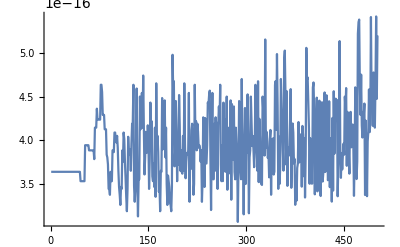

```mathematica
ListLinePlot[ηtest]
```

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
```

```mathematica
Jηeqnx = D[ηeqn, {qx}];
cJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[Jηeqnx]];
```

```mathematica
Jηeqnxtest = Table[Norm[cJηeqnx@@qsol[i].qsol'[i]],{i, 0, 0.5, 0.001}];
```

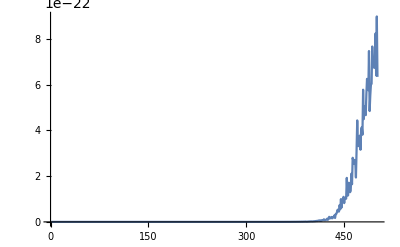

```mathematica
ListLinePlot[Jηeqnxtest, PlotRange->All]
```

```mathematica
(*3. Second order check: Cheking norm of Jηq.d2q+dJηq.dq*)
```

```mathematica
dJηeqnx = D[Jηeqnx/.qrule, t];
dJηeqnx2 = dJηeqnx/.rqrule;
```

```mathematica
cdJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}}, Evaluate[dJηeqnx2]];
```

```mathematica
dJηeqnxtest = Table[Norm[cJηeqnx@@qsol[i].qsol''[i]+cdJηeqnx@@Join[qsol[i], qsol'[i]].qsol'[i]],{i, 0, 0.5, 0.001}];
```

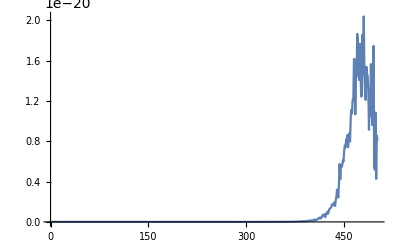

```mathematica
ListLinePlot[dJηeqnxtest, PlotRange->All]
```

```mathematica
(*To check Energy remove the applied external torque*)
```

```mathematica
(*4. Energy: Checking Energy constant criteria*)
```

```mathematica
Vsubs = V/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Msubs = TrigExpand[Mmat]/.rqrule/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
```

```mathematica
Vlist = Table[Vsubs/.Inner[Rule,qx, qsol[i], List], {i, 0, 0.5, 0.001}];
Mlist = Table[Msubs/.Inner[Rule,qx, qsol[i], List], {i, 0, 0.5, 0.001}];
qfull = Table[Join[qsol[i], iksol[qsol[i]]],{i, 0,0.5, 0.001}];
```

```mathematica
Jηqtab = Table[cJηq@@qfull[[i]],{i, Length[qfull]}];
Jηxtab = Table[cJηx@@qfull[[i]],{i, Length[qfull]}];
```

```mathematica
Jqxtab = Table[-Inverse[Jηqtab[[i]]].Jηxtab[[i]], {i, Length[qfull]}];
dq2 = Table[qsol'[i], {i, 0,0.5, 0.001}];
dqtab = Table[Join[dq2[[i]], Jqxtab[[i]].dq2[[i]]],{i, Length[dq]}];
Hlist = Table[1/2*(dqtab[[i]].Mlist[[i]].dqtab[[i]])+Vlist[[i]],{i, Length[dq]}];
H1 = ConstantArray[Hlist[[1]], Dimensions[Hlist]];
```

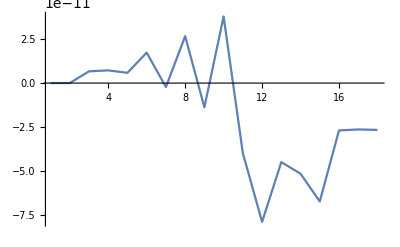

```mathematica
ListLinePlot[(Hlist-H1)/H1, PlotRange->All]
```

```mathematica
qvals = Table[Inner[Rule, q, Join[qsol[i],iksol[qsol[i]]], List],{i, 0,0.45, 0.0001}];
```

```mathematica
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*Plotter*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, llinks, jointstop, jointsbase]]
```

```mathematica
Join[qx/.samplex, iksol[qx/.samplex]]
```

{0,0,0.75,0,0,0,-0.255403,-0.381148,0.58466,0.58466,-0.381148,-0.255403,0.535692,0.459341,-0.0671288,0.0671288,-0.459341,-0.535692,0.901419,0.901419,0.901419,0.901419,0.901419,0.901419}

```mathematica
plotsrspm[]
```

plotsrspm[]

```mathematica
mansrspm = Manipulate[
plotsrspm[qvals[[j]]],
{j, 1, Length[qvals], 1}, ContentSize->{400,400}];
```

```mathematica
(*Now the dynamics is set alright to the expected dynamics. Moving into controls, we would need actuator space dynamics for that.*)
```

```mathematica
(*Formulating the Jacobians for mapping the dynamics to actuator space*)
```

```mathematica
Jηθ = D[η, {l}];
Jηxϕ= D[η, {Join[qx, ϕ, ψ]}];
```

```mathematica
tJηθ = Jηθ;
```

```mathematica
cJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηθ]];
```

```mathematica
dJηθ = D[Jηθ/.qrule, t]/.rqrule;
```

```mathematica
cdJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηθ]];
```

```mathematica
tJηxϕ = Jηxϕ;
```

```mathematica
cJηxϕ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηxϕ]];
```

```mathematica
dJηxϕ = D[Jηxϕ/.qrule, t]/.rqrule;
```

```mathematica
cdJηxϕ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηxϕ], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
(*Dynamics in joint space*)
```

```mathematica
cη = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[η], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
tempJn = D[η, {Join[qx, ϕ, ψ]}];
cJn = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tempJn], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJn@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
lsample = iksol[qsol[0.1]][[13;;18]];
ϕsample = Join[qsol[0],iksol[qsol[0]][[1;;12]]];
ϕactual = Join[qsol[0.1],iksol[qsol[0.1]][[1;;12]]];
```

```mathematica
(*Verifying the module*)
```

```mathematica
Max[Abs[ϕactual - TrackRoot[lsample, ϕsample]]]
```

7.21645×10^-16

```mathematica
(*We'll need a root tracker for FK computation*)
```

```mathematica
tempxϕ = Join[qsol[0], iksol[qsol[0]]][[1;;18]];
doubledotsac[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{bla, Mval, Cval, Gval, LHS, dqe, qe, Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval},
(*Perform FK for the configuration and task space variables*)
(*bla= AbsoluteTiming[TrackRoot[q, tempxϕ]];*)
(*Print[bla[[1]]];*)
(*tempxϕ = bla[[2]];*)
tempxϕ = TrackRoot[q, tempxϕ];
qe = Join[tempxϕ,q];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
LHS = -(Inverse[Mθval]).(Cθval.dq+Gθval);
Return[LHS];
];
```

```mathematica
θinit = iksol[qsol[0.0001]][[13;;18]];
dθinit = ConstantArray[0,{6}];
```

```mathematica
d2θinit = doubledotsac[θinit, dθinit]
```

{-9.0204,-9.02041,-9.0204,-9.0204,-9.02041,-9.0204}

```mathematica
(*Clear[tempxϕ]*)
tempxϕ = Join[qsol[0], iksol[qsol[0]]][[1;;18]];
tic[]
dynsimac = NDSolve[{doubledotsac[q1[t],q1'[t]]==q1''[t],q1[0]==θinit,q1'[0]==dθinit},q1,{t,0,0.47},AccuracyGoal->15, Method->"Adams"][[1]]
toc[]
```

{q1→InterpolatingFunction[{{0., 0.47}}, <>]}

Actual time consumed: 1 minutes, 14.468663 seconds.

Actual time consumed: 74.468663 seconds.

CPU time consumed: 1 minutes, 13.625 seconds.

CPU time consumed: 73.625 seconds.

```mathematica
qsolac = q1/.dynsimac;
```

```mathematica
θac = Table[Mean[qsolac[i]],{i, 0, 0.469, 0.001}];
```

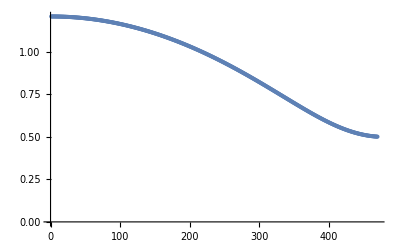

```mathematica
ListPlot[θac]
```

```mathematica
(*When the top platform overlaps with the bottom platform, the leg lengths are as below. This is the minimum leg length*)
```

```mathematica
qsolac[0.47]
```

{0.500996,0.500971,0.501104,0.501104,0.500971,0.500996}

```mathematica
Table[Norm[((b - al)/.datap)[[i]]],{i, 6}]
```

{0.500056,0.500056,0.500056,0.500056,0.500056,0.500056}

```mathematica
(*When using Adams solver it takes a lot of time to solve *)
```

```mathematica
trackedxϕ = ϕsample;
qvalsac={Join[ϕsample, θinit]};
dqθ = {dθinit};
d2qθ = {d2θinit};
```

```mathematica
For[i=0, i≤0.47, i=i+0.001,
trackedxϕ = TrackRoot[qsolac[i], trackedxϕ];
AppendTo[qvalsac,Join[trackedxϕ, qsolac[i]]];
AppendTo[dqθ, qsolac'[i]];
AppendTo[d2qθ, qsolac''[i]];
]
```

```mathematica
qxdat = Reap[Do[Sow[qvalsac[[i]][[1;;6]]],{i, Length[qvalsac]}]][[2]][[1]];
```

```mathematica
(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)
```

```mathematica
ηtest = Table[Norm[ηeqn/.Inner[Rule,qx,qxdat[[i]], List]],{i, Length[qvalsac]}];
```

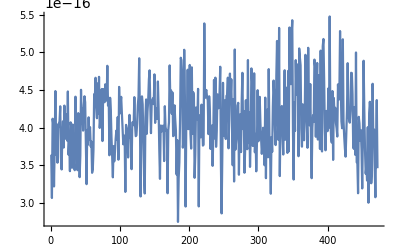

```mathematica
ListLinePlot[ηtest, PlotRange->All]
```

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
```

```mathematica
dqe = Table[Join[(-Inverse[ (cJηxϕ@@qvalsac[[i]])].cJηθ@@qvalsac[[i]]).dqθ[[i]], dqθ[[i]]], {i, Length[qvalsac]}];
dqxdat = Reap[Do[Sow[dqe[[i]][[1;;6]]],{i, Length[dqe]}]][[2]][[1]];
```

```mathematica
Jηeqnxtest = Table[Norm[cJηeqnx@@qxdat[[i]].dqxdat[[i]]],{i,Length[qxdat]}];
```

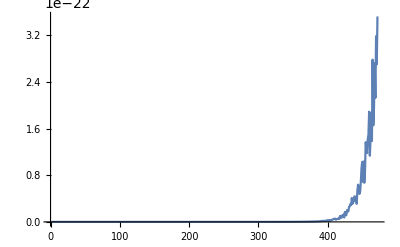

```mathematica
ListLinePlot[Jηeqnxtest, PlotRange->All]
```

```mathematica
(*dJηeqnxtest = Table[Norm[cJηeqnx@@qxdat[[i]].qsol''[i]+cdJηeqnx@@Join[qxdat[[i]], dqxdat[[i]]].dqxdat[[i]]],{i,Length[qxdat]}];*)
```

```mathematica
ListLinePlot[dJηeqnxtest, PlotRange->All]
```

-Graphics-

```mathematica
d2qe = Table[
Jηxϕval = cJηxϕ@@qvalsac[[i]];
Jηθval = cJηθ@@qvalsac[[i]];
dJηxϕval = cdJηxϕ@@Join[qvalsac[[i]], dqe[[i]]];
dJηθval = cdJηθ@@Join[qvalsac[[i]], dqe[[i]]];
ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {IdentityMatrix[6]}}].d2qθ[[i]], {i, Length[d2θinit]}];
```

```mathematica
(*We need second derivative of x for the third check*)
```

```mathematica
(*To check Energy remove the applied external torque*)
```

```mathematica
(*4. Energy: Checking Energy constant criteria*)
```

```mathematica
Vlistac = Table[Vsubs/.Inner[Rule,qx,qxdat[[i]], List], {i, Length[qxdat]}];
Mlistac = Table[Msubs/.Inner[Rule,qx, qxdat[[i]], List], {i,  Length[qxdat]}];
```

```mathematica
Hlistac = Table[1/2*(dqe[[i]].Mlistac[[i]].dqe[[i]])+Vlistac[[i]],{i, Length[dqe]}];
H1ac = ConstantArray[Hlistac[[1]], Dimensions[Hlistac]];
```

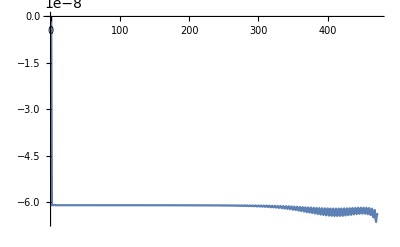

```mathematica
ListLinePlot[(Hlistac-H1ac)/H1ac, PlotRange->All]
```

```mathematica
(*Second order check needs to be done*)
```

```mathematica
(*Trajectory Tracking Control*)
```

```mathematica
d2x2d2qe[qx_, dqx_, d2qx_]:= Module[{Jηqval, Jηxval, Jqxval, dJηqval, dJηxval, dqe, Jqexval, dJqexval, d2qeval, qe},
qe = Join[qx, iksol[qx]];
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dqx, Jqxval.dqx];
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
Jqexval = ArrayFlatten[{{IdentityMatrix[6]}, {Jqxval}}];
dJqexval = ArrayFlatten[{{ConstantArray[0,{6,6}]}, {-Inverse[Jηqval].(-dJηqval.Inverse[Jηqval].Jηxval+dJηxval)}}];
d2qeval = dJqexval.dqx+Jqexval.d2qx;
Return[{dqe, d2qeval}];
]
```

```mathematica
qe2dqe[qe_, dθ_]:= Module[{dqe, Jηxϕval, Jηθval, Jxϕθval},
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dθ, dθ];
Return[dqe];
]
```

```mathematica
(*To recover the required τ*)
```

```mathematica
findτ[qe_, dqe_, τdash_]:=Module[{Jηxϕval, Jηθval, Jxϕθval, Mval, Cval, Gval, Mθval, Cθval, Gθval, Jqeθval, dJqeθval, τval, dθval, dθival},
(*Getting the velocities of the configuration space variables*)
dθival = dqe[[19;;24]];
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*Mapping it to the required actuator torques*)
τval = (Mθval.τdash)+Cθval.dθival+Gθval;
Return[τval]
]
```

```mathematica
(*We assume that we are within the SWZ. We try to track a 3D-Lissajous Curve with no change in c1, c2, c3*)
```

```mathematica
scale = 4;
xparam = xp*Sin[ωx*t-δx]/.{xp->.6/scale, ωx->1/5, δx->π/2};
yparam = yp*Sin[ωy*t-δy]/.{yp->.3/scale, ωy->4/5, δy->0};
zparam = 1+zp*Sin[ωz*t-δz]/.{zp->.2/scale, ωz->2/5, δz->π/2};
ParametricPlot3D[{xparam, yparam, zparam},{t, 0,5*2π}];
```

```mathematica
xtrack = {xparam, yparam, zparam, 0,0,0};
dxtrack = D[{xparam, yparam, zparam, 0,0,0}, t];
d2xtrack = D[{xparam, yparam, zparam, 0,0,0}, {t, 2}];
```

```mathematica
h = 0.001;
tf = 10*2π;
```

```mathematica
(*Getting the task space desired data*)
```

```mathematica
xtrackdat = Table[N[xtrack/.{t->i}],{i, 0, tf, h}];
dxtrackdat = Table[N[dxtrack/.{t->i}],{i, 0, tf, h}];
d2xtrackdat = Table[N[d2xtrack/.{t->i}],{i, 0, tf,h}];
```

```mathematica
Manipulate[Show[plotsrspm[Inner[Rule, q, Join[xtrackdat[[i]], iksol[xtrackdat[[i]]]], List]], ListPointPlot3D[xtrackdat[[1;;i, 1;;3]], PlotStyle->Red]], {i, 1, Length[xtrackdat], 1}];
```

```mathematica
(*Getting the joint space desired data*)
```

```mathematica
qddat = Table[iksol[xtrackdat[[i]]],{i, Length[xtrackdat]}];
θddat = qddat[[;;, 13;;18]];
```

```mathematica
θdinit = θddat[[1]];
dθdinit = d2x2d2qe[xtrackdat[[1]],xtrackdat[[1]] , {0,0,0,0,0,0}][[1]][[19;;24]];
```

```mathematica
(*For now the controller gains are kp and 2√kp (as given in Sadiq et. al.), so that it is critically damped*)
```

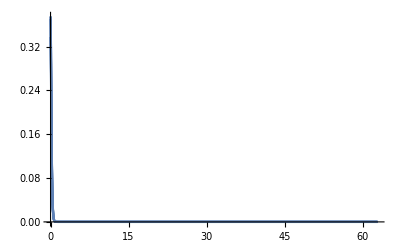

```mathematica
controlparams = {kp->100, kv->2*10};
Kp = kp*IdentityMatrix[6]/.controlparams;
Kv = kv*IdentityMatrix[6]/.controlparams;
(*Module for error dynamics*)
errordyn=NDSolve[{e''[t]+Kp.e[t]+Kv.e'[t]==0,e[0]==θdinit/3,e'[0]==dθdinit/3},e,{t,0,tf}][[1]];
Plot[e[t]/.errordyn,{t, 0, tf}, PlotRange->All]
```

```mathematica
(*Now sampling the errors*)
```

```mathematica
edat = Table[e[t]/.errordyn, {t, 0, tf, h}];
dedat = Table[e'[t]/.errordyn, {t, 0, tf, h}];
```

```mathematica
(*Finding the desired extended configuration variable*)
```

```mathematica
dqeddat = Table[d2x2d2qe[xtrackdat[[i]],dxtrackdat[[i]], d2xtrackdat[[i]]][[1]],{i, Length[xtrackdat]}];
d2qeddat = Table[d2x2d2qe[xtrackdat[[i]], dxtrackdat[[i]], d2xtrackdat[[i]]][[2]],{i, Length[xtrackdat]}];
```

```mathematica
dθddat = Table[dqeddat[[i]][[19;;24]],{i, Length[dqeddat]}];
d2θddat = Table[d2qeddat[[i]][[19;;24]],{i, Length[dqeddat]}];
```

```mathematica
τdash = Table[d2θddat[[i]]+Kp.edat[[i]]+Kv.dedat[[i]],{i, Length[edat]}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Finding the configurations corresponding to the controller*)
```

```mathematica
θidat = θddat-edat;
```

$Aborted

```mathematica
Clear[i];
tempinit = Join[taskddat[[1]], iksol[taskddat[[1]]]][[1;;18]];
qeidat = Table[tempinit = TrackRoot[θidat[[i]], tempinit];
Join[TrackRoot[θidat[[i]], tempinit], θidat[[i]]],{i, Length[θidat]}];
```

```mathematica
dqeidat = Table[qe2dqe[qeidat[[i]], dθidat[[i]]],{i, Length[dθidat]}];
```

```mathematica
τvals = Table[findτ[qeidat[[i]], dqeidat[[i]], τdash[[i]]], {i, Length[qeidat]}];
```

Part::partw: Part 1 of {} does not exist.

Part::take: Cannot take positions 19 through 24 in {}⟦1⟧.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 48 of the argument template.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 48 of the argument template.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

CompiledFunction::cfct: Number of arguments 2 does not match the length 48 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Dot::dotsh: Tensors {{70.4292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,70.4292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,70.4292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«19»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,11.6175,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,11.6175}} and {{-«1»,«4»,-{{0.105294,0.166014,-0.253277,-0.373077,-0.375987,0.660406,-0.232217,-0.0350689,-0.407129,-0.232217,0.0350689,-0.407129,-0.373077,0.375987,0.660406,0.105294,-0.166014,-0.253277},«16»,{0.505574,0.797122,-1.21612,-0.162996,-0.164267,0.288529,«6»,0.162996,-0.164267,-0.288529,-0.505574,-0.518294,1.21612}}.(«1»)},«6»} have incompatible shapes.

Part::partw: Part 2 of {} does not exist.

Part::take: Cannot take positions 19 through 24 in {}⟦2⟧.

Dot::dotsh: Tensors {{70.4292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,70.4292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,70.4292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«19»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,11.6175,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,11.6175}} and {{-«1»,«4»,-{{0.105295,0.166,-0.253281,-0.37308,-0.375951,0.660418,-0.232215,-0.0350913,-0.407137,-0.232215,0.0350466,-0.407137,-0.37308,0.376023,0.660418,0.105295,-0.166028,-0.253281},«16»,{0.50557,0.797042,-1.21612,-0.162994,-0.164248,0.288529,«6»,0.162994,-0.16428,-0.288529,-0.50557,-0.518219,1.21612}}.(«1»)},«6»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 19 through 24 in {}⟦3⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

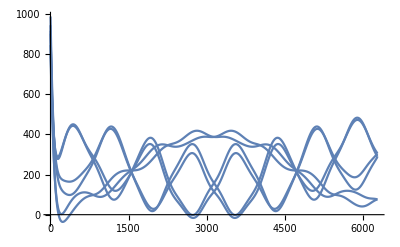

```mathematica
Show[Table[ListLinePlot[τvals[[;;, i]]],{i,6}], PlotRange->All]
```

```mathematica
cartacc = Table[d2qeidat[[i]][[1;;3]], {i, Length[d2qeidat]}];
```

```mathematica
(*Max cartesian accelerations*)
```

```mathematica
{Max[Abs[cartacc[[;;,1]]]], Max[Abs[cartacc[[;;,2]]]], Max[Abs[cartacc[[;;,3]]]]}
```

{0.848528,4.94773,0.894427}

```mathematica
(*So, these are the required torques from the feedback linearised model. We need to simulate it and validate it against the required data*)
```

```mathematica
(*Ideally the torques should be say in zero order hold until the next control loop. But here we fit an interpolation function to the torques*)
```

```mathematica
time = Table[i, {i, 0, tf, h}];
τvalswitht = Table[Transpose[ArrayFlatten[{time, τvals[[;;, i]]}]],{i, 6}];
τfuncs = Table[Interpolation[τvalswitht[[i]]],{i, 6}];
```

```mathematica
(*Now we have the torques at each instant, let us simulate the system with these inputs*)
```

```mathematica
tempxϕ = qeidat[[1]][[1;;18]];
doubledotscontrol[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&), t_]:=Module[{bla, Mval, Cval, Gval, LHS, dqe, qe, Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval, τθval},
(*Perform FK for the configuration and task space variables*)
(*bla= AbsoluteTiming[TrackRoot[q, tempxϕ]];*)
(*Print[bla[[1]]];*)
(*tempxϕ = bla[[2]];*)
tempxϕ = TrackRoot[q, tempxϕ];
qe = Join[tempxϕ,q];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
τθval = {τfuncs[[1]][t], τfuncs[[2]][t], τfuncs[[3]][t], τfuncs[[4]][t], τfuncs[[5]][t], τfuncs[[6]][t]};
LHS = (Inverse[Mθval]).(τθval-Cθval.dq-Gθval);
(*LHS = (Inverse[Mθval]).(-Cθval.dq-Gθval);*)
Return[LHS];
];
```

```mathematica
θinitc = θidat[[1]];
dθinitc = dθidat[[1]];
```

```mathematica
d2θinitc = doubledotsac[θinitc, dθinitc]
```

{-7.12739,-6.9715,-7.66258,-7.66258,-6.9715,-7.12739}

```mathematica
(*Clear[tempxϕ]*)
tempxϕ = qeidat[[1]][[1;;18]];
tic[]
controlsim = NDSolve[{doubledotscontrol[q1[t],q1'[t],t]==q1''[t],q1[0]==θinitc,q1'[0]==dθinitc},q1,{t,0,0.5}, AccuracyGoal->15,Method->"Adams"][[1]];
toc[]
```

Actual time consumed: 0.195967 seconds.

CPU time consumed: 0.188 seconds.

```mathematica
qcontrol = q1/.controlsim;
```

```mathematica
(*Non-linear dynamics decoupling approach is another name for feedback linearisation*)
```